```mathematica
hist = HistogramList[{0.15, 0.30, 0.40, 0.25}, {{2021, 2032, 2050, 2100, 2500}}, "PDF"]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{2021,2032,2050,2100,2500},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

```mathematica
hist
```

{{2021,2032,2050,2100,2500},{0,0,0,0}}

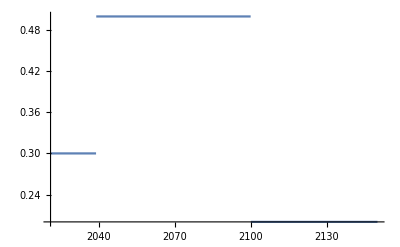

```mathematica
{{2021,2032,2050,2100,2500},{0,0,0,0}}
Plot[Piecewise[{{0.3/(2039-2021),2021<=x<=2039},{0.5, 2039 < x <= 2100},{0.2, 2100<= x }}],{x, 2021, 2150}]
```

```mathematica
f[Subscript[x, b], Subscript[α, b],Subscript[η, b]]:= Subscript[α, b]*Subscript[x, b]^(1 - Subscript[η, b])/(1 - Subscript[η, b])
```

```mathematica
f[Subscript[x, b], Subscript[α, b],Subscript[η, b]]
```

(x_b^(1-η_b) α_b)/(1-η_b)

```mathematica
f[Subscript[x, o], Subscript[α, o],Subscript[η, o]]:= Subscript[α, o]*Subscript[x, o]^(1 - Subscript[η, o])/(1 - Subscript[η, o])
```

```mathematica
p[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o], t] := Exp[-Integrate[(1 - f[Subscript[x, b], Subscript[α, b],Subscript[η, b]])*Subscript[δ, b][τ]+ (1 - f[Subscript[x, o], Subscript[α, o],Subscript[η, o]])*Subscript[δ, o][τ]+ Subscript[δ, AI][τ] , {τ, 0, t}]]
```

```mathematica
p[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o], t]
```

ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ)

```mathematica
x = Subscript[x, AI] + Subscript[x, b] + Subscript[x, o]
δ[t_]:= Subscript[δ, AI][t] + Subscript[δ, b][t] + Subscript[δ, o][t]
ϕ[t_, B_, Subscript[ϕ, 0], Subscript[δ, 0]]:=Subscript[ϕ, 0]*B*(δ[t]/Subscript[δ, 0]) 
H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t] = p[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o], t]*(a + b*Subscript[x, AI]^(1 - Subscript[η, AI])/(1 - Subscript[η, AI]))*Subscript[δ, AI][t] + v*(r*m-(Subscript[x, AI] + Subscript[x, b] + Subscript[x, o]) + ϕ[t])
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x=x_AI+x_b+x_o]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[H[δ_AI,δ_b,δ_o,x_b,α_b,η_b,x_o,α_o,η_o,a,b,x_AI,v,m,ϕ_0,B,δ,t]=p[δ_AI,δ_b,δ_o,x_b,α_b,η_b,x_o,α_o,η_o,t] (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]+v (r m-x+ϕ[t])]

```mathematica
x = Subscript[x, AI] + Subscript[x, b] + Subscript[x, o]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x=x_AI+x_b+x_o]

```mathematica
x
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x_AI+x_b+x_o]

```mathematica
δ[t_]:= Subscript[δ, AI][t] + Subscript[δ, b][t] + Subscript[δ, o][t]
```

```mathematica
ϕ[t_, B_, Subscript[ϕ, 0], Subscript[δ, 0]]:=Subscript[ϕ, 0]*B*(δ[t]/Subscript[δ, 0])
H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t] = p[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o], t]*(a + b*Subscript[x, AI]^(1 - Subscript[η, AI])/(1 - Subscript[η, AI]))*Subscript[δ, AI][t] + v*(r*m-(Subscript[x, AI] + Subscript[x, b] + Subscript[x, o]) + ϕ[t])
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[H[δ_AI,δ_b,δ_o,x_b,α_b,η_b,x_o,α_o,η_o,a,b,x_AI,v,m,ϕ_0,B,δ,t]=p[δ_AI,δ_b,δ_o,x_b,α_b,η_b,x_o,α_o,η_o,t] (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]+v (r m-(x_AI+x_b+x_o)+ϕ[t])]

```mathematica
Subscript[x, AI]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x_AI]

```mathematica
Subscript[x, b]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

```mathematica
Clear[Subscript[x, AI]]
```

Clear::ssym: x_AI is not a symbol or a string.

```mathematica
Subscript[x, AI]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x_AI]

```mathematica
Subscript[x, b]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x_b]

```mathematica
Subscript[x, o]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x_AI.

Hold[x_o]

```mathematica
Clear[x]
```

```mathematica
Subscript[x, AI]
```

x_AI

```mathematica
Subscript[x, o]
```

```mathematica
ϕ[t_, B_, Subscript[ϕ, 0], Subscript[δ, 0]]
```

```mathematica
(B_ Subscript[ϕ, 0] (Subscript[δ, AI][t_]+Subscript[δ, b][t_]+Subscript[δ, o][t_]))/Subscript[δ, 0]
H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t] = p[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o], t]*(a + b*Subscript[x, AI]^(1 - Subscript[η, AI])/(1 - Subscript[η, AI]))*Subscript[δ, AI][t] + v*(r*m-(Subscript[x, AI] + Subscript[x, b] + Subscript[x, o]) + ϕ[t])
```

(B_ ϕ_0 (δ_AI[t_]+δ_b[t_]+δ_o[t_]))/δ_0

v (m r-x_AI-x_b-x_o+ϕ[t])+ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]

```mathematica
H
```

H

```mathematica
D[H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t], Subscript[x, AI]]
```

-v+b ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) x_AI^-η_AI δ_AI[t]

```mathematica
D[H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t], Subscript[x, b]]
```

-v-ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) (∫_0^t -x_b^-η_b α_b δ_b[τ]ⅆτ) (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]

```mathematica
D[H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t], Subscript[x, o]]
```

-v-ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) (∫_0^t -x_o^-η_o α_o δ_o[τ]ⅆτ) (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]

```mathematica
Solve[D[H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t], Subscript[x, AI]]==0, Subscript[x, AI]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x_AI→((ⅇ^(∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) v)/(b δ_AI[t]))^(-1/η_AI)}}

```mathematica
Solve[D[H[Subscript[δ, AI],Subscript[δ, b],Subscript[δ, o],Subscript[x, b], Subscript[α, b],Subscript[η, b],Subscript[x, o], Subscript[α, o],Subscript[η, o],a,b,Subscript[x, AI],v,m,Subscript[ϕ, 0],B, δ, t], Subscript[x, b]]==0, Subscript[x, b]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[-v-ⅇ^(-∫_0^t (Subscript[δ, AI][τ]+(1-(Subscript[x, b]^(1-Subscript[η, b]) Subscript[α, b])/(1-Subscript[η, b])) Subscript[δ, b][τ]+(1-(Subscript[x, o]^(1-Subscript[η, o]) Subscript[α, o])/(1-Subscript[η, o])) Subscript[δ, o][τ])ⅆτ) (∫_0^t -Subscript[x, b]^(-Subscript[η, b]) Subscript[α, b] Subscript[δ, b][τ]ⅆτ) (a+(b Subscript[x, AI]^(1-Subscript[η, AI]))/(1-Subscript[η, AI])) Subscript[δ, AI][t]==0,Subscript[x, b]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-v-ⅇ^(-∫_0^t (δ_AI[τ]+(1-(x_b^(1-η_b) α_b)/(1-η_b)) δ_b[τ]+(1-(x_o^(1-η_o) α_o)/(1-η_o)) δ_o[τ])ⅆτ) (∫_0^t -x_b^-η_b α_b δ_b[τ]ⅆτ) (a+(b x_AI^(1-η_AI))/(1-η_AI)) δ_AI[t]==0,x_b]

```mathematica
p[t_]:=Piecewise[{{0.20/(2039-2021),2021<= t< 2039},{0.50/(2100-2039),2039<=t<2100},{0.20/(2500-2100),2100<=t<2500}}]
```

```mathematica
p[t]
```

Piecewise[{{0.0111111, 2021≤t<2039}, {0.00819672, 2039≤t<2100}, {0.0005, 2100≤t<2500}, {0, True}}]

```mathematica
distrib = ProbabilityDistribution[Piecewise[{{0.20/(2039-2021),2021<= t< 2039},{0.50/(2100-2039),2039<=t<2100},{0.20/(2500-2100),2100<=t<2500}}],{t,2021, Infinity}]
```

ProbabilityDistribution[Piecewise[{{0.0111111, 2021≤x<2039}, {0.00819672, 2039≤x<2100}, {0.0005, 2100≤x<2500}, {0, True}}],{x,2021,∞}]

```mathematica
pdf = PDF[distrib, x]
```

Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}]

```mathematica
pdf
```

Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}]

```mathematica
Histogram[pdf, 200]
```

Histogram::ldata: Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}] is not a valid dataset or list of datasets.

Histogram[Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}],200]

```mathematica
data = RandomVariate[pdf,10]
```

RandomVariate::udist: The specification Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}] is not a random distribution recognized by the system.

RandomVariate[Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}],10]

```mathematica
RandomVariate[pdf]
```

RandomVariate::udist: The specification Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}] is not a random distribution recognized by the system.

RandomVariate[Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}]]

```mathematica
Integrate[pdf[t],{t,2021, Infinity}]
```

∫_2021^∞ (Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}])[t]ⅆt

```mathematica
pdf
```

Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}]

```mathematica
f[x_]:=Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672131147541, 2039≤x<2100}, {0.011111111111111112, 2021<x<2039}, {0, True}}]
```

```mathematica
Integrate[f[x],{x,2021, Infinity}]
```

0.9

```mathematica
RandomVariate[f[x],10]
```

RandomVariate::udist: The specification Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}] is not a random distribution recognized by the system.

RandomVariate[Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}],10]

```mathematica
Histogram[f[x]]
```

Histogram::ldata: Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}] is not a valid dataset or list of datasets.

Histogram[Piecewise[{{0.0005, 2100≤x<2500}, {0.00819672, 2039≤x<2100}, {0.0111111, 2021<x<2039}, {0, True}}]]

```mathematica
distrib = 0.20 * UniformDistribution[{2021,2039}]+ 0.50*  UniformDistribution[{2039,2100}] + 0.30* UniformDistribution[{2100,Infinity}]
```

0.2 UniformDistribution[{2021,2039}]+0.5 UniformDistribution[{2039,2100}]+0.3 UniformDistribution[{2100,∞}]

```mathematica
Histogram[distrib]
```

Histogram::ldata: 0.2 UniformDistribution[{2021,2039}]+0.5 UniformDistribution[{2039,2100}]+0.3 UniformDistribution[{2100,∞}] is not a valid dataset or list of datasets.

Histogram[0.2 UniformDistribution[{2021,2039}]+0.5 UniformDistribution[{2039,2100}]+0.3 UniformDistribution[{2100,∞}]]

```mathematica
RandomVariate[UniformDistribution[{2021,2039}]]
```

2028.21

```mathematica
DSolve[{p'[t]== - p[t] δ[t]+ δ[t],p[0]==0}, p[t],t]
```

{{p[t]→ⅇ^(-δ[K[1]]K[1]0t) ⅇ^(--δ[K[1]]K[1]0K[2]) δ[K[2]]K[2]0t}}